```mathematica
yinf = 0.650;
x0 = 0.005;
fi[x_]:=Integrate[y^2/Sqrt[x^2+y^2],{y, 0, yinf}, Assumptions->{x≥0, yinf>0}];
f[x_]:=x-x0 - 3fi[x];
Plot[f[x], {x, 0, 1}]
FindRoot[f[z], {z, 0.4}]
```

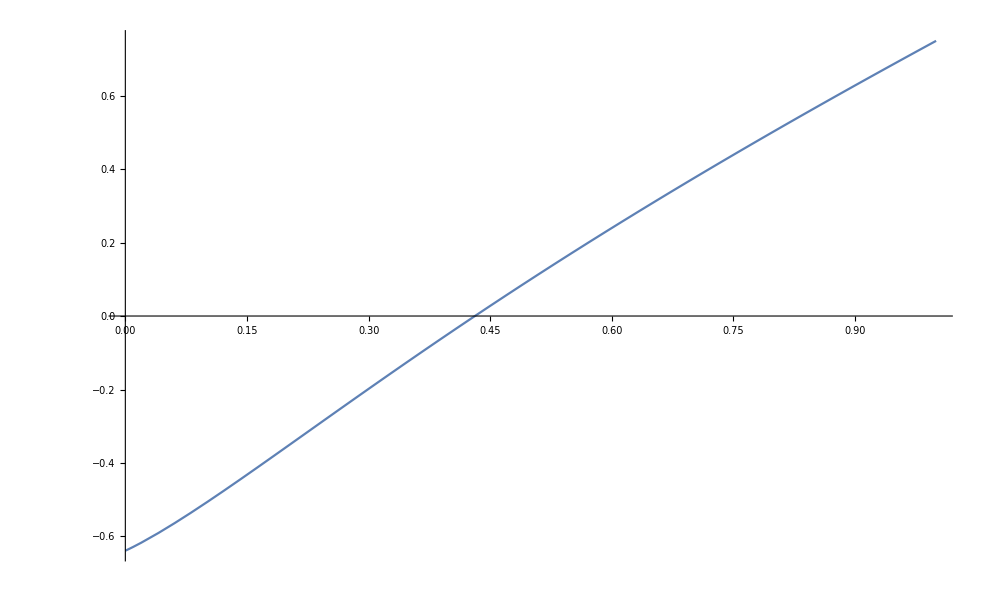

```mathematica
{z->0.43116952523245355}
```

Set::write: Tag Times in (0 0 0.65)/n is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.